FittedModel[-0.296612+0.0033636 x+0.0000845375 x^2]

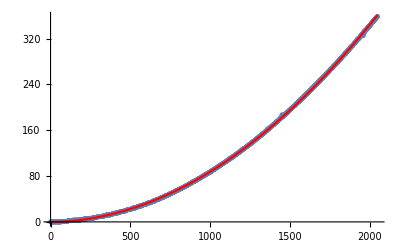

0.99998

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "join-fixed"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x+c*x^2,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```